# Wealth, IQ, and a Monte Carlo Economy

## Version 0.1

## Introduction

### Purpose:

The purpose of this notebook is to explore an objection Nassim Nicholas Taleb raised regarding IQ as a valid measure of intelligence.  It’s also largely a means to gain some experience with Mathematica, stochastic modeling, and the process of using a notebook as means to communicate code, documentation, analysis, and prose.  What follows is a work in progress and largely a tool for my self-education.  There are likely errors.

### Caveats:

It should be emphasized that I am not a specialist, nor even particularly well versed in any of the concepts which intersect this subject (including but is not limited to, intelligence research, psychology, economics, probability, statistics, stochastic modeling, game theory, etc).  I’m just an armchair contrarian equipped with a for loop and a random number generator. Still, I hope to make a relevant point.

### Taleb’s Primary Objection:

Taleb has several objections to the utility of IQ as a means of measuring intelligence. The most important, I think, goes like this
  1) IQ measures with psychologists define as intelligence (psych-Int)
  2) this laboratory notion of psych-Int has little to do with the real world (real-Int)
  3) real world intelligence is survivability
Here survivability should be mostly thought of, I think, in a financial-trader sense, rather than, say, the ability to start a fire with just sticks and to live off the land in post apocalyptic setting. 

The evidence Taleb provides seems to be more theoretical than empirical, highlighting potential (if not likely) probability and statistics errors.  The data sets which best make his case though, seem to be comparing a person’s wealth to their IQ.  Visual inspection shows the scatterplot to be incredibly noisy, and perhaps non-linear, with what seems to be little utility for people with above average IQ.

### My Rebuttal in Brief:

My counter-argument is to model a (very simplistic) economy via gambling, the output of which is a data set which shows that
  1) Wealth as a function of “intelligence” is very noisy and non-linear.
  2)

### Method Overview:

In brief, we model an economy in which every transaction is a zero-sum game played by a pair of people. There is a pool of games from which pairs of players are allowed draw, and these games are allowed to be asymmetric and biased in regards to both probability of a player winning, and the expected value of their winnings. Players are randomly matched, and each player decides to play any given game by estimating the expected value of their winnings from the game, with more “intelligent” people (by definition) making more accurate predictions on average.  After each game is played, the loser of that game re-computes their expected winnings, and if positive they play again (in particular, the winner does not re-compute expected winnings).  After every pair resolves their game, a round is considered complete.  After fifty consecutive rounds are played the final wealth of each player is recorded. This completes a “history.” Players wealth is reset to starting values, and the process is repeated to complete one-hundred histories. The mean ending-wealth of each player is then computed, and scatter plots are provided.

In the current version, constants are chosen so that 1) each player begins with 50,000 dollars, 2) no player is willing to lose more than 20% of their current wealth in a single game, 3) each round, each player is matched with about 10% of the rest of the population to play a game, although if either player doesn’t have positive expected winnings, then the game is not played, 4) the total population size is 300 players.

## Model Specifications

### Definition of Variables

player -- A player consists of tuple (W, g, o, r), where

W -- W is a non-negative number measuring a player’s total wealth.

g -- g is the measure of intelligence. It is normally distributed among the population of players, with mean 0 and standard deviation 1.

o -- is a real number measuring “optimism,” which biases players’ estimates of likelihood of winning games: players with more positive o tend to overestimate the probability they will win games; players with more negative o tend to underestimate the probability they will win games.

r -- r is a measure of “riskiness.” Players with high r are willing to risk losing a larger percentage of their wealth in any single given game.

game -- A game consists of a triple (p, A, B), where

p -- p is the probability that Player 1 will win (the probability that Player 2 will win is 1-p)

A -- A is the amount that Player 2 will pay Player 1 if Player 1 wins

B -- B is the amount that Player 1 will pay Player 2 if Player 2 wins

mu -- mu is the probability that a mutation occurs when a game is replicated

matchProb -- matchProb is the probability that a pair of players will be matched to play a game; this does not account for the probability that they will decide not to play after expected winnings are computed.

round --

gamePool -- gamePool is a list of games played on a given round

### Initialize Constants

We start by initializing our global parameters.

```mathematica
playerPopSize=300;  (* Set the total size of the player population *)
startingWealth=50000.0;  (* each player's starting wealth *)
matchProb=0.1;
rematches=SparseArray[{},{playerPopSize,playerPopSize}];
roundMax=50;
maxError=0.8;
minError=0.1;
maxHistories=100;
```

Here we initialize the base games that players can always choose to play. The games are all zero sum, but the expected value of either Players’ winnings need not be zero.

```mathematica
baseP={0.5,0.25,0.1,0.02};
baseGames=Flatten[Table[{baseP[[i]],(1.0+k*0.1)*(1-baseP[[i]])*10^j/(baseP[[i]]),(1.0-k*0.1)*10^j},{i,1,4},{j,1,4},{k,-3,3}],2];
(*  The was for testing purposes.
b=baseGames; 
Table[b[[i]][[1]]*b[[i]][[2]] -(1-b[[i]][[1]])*b[[i]][[3]],{i,1,Length[b]}];
*)
```

Here we define estProb[g,q] which takes a players’ intelligence “g” and probability “q” and returns that player’s estimate of “q.”

```mathematica
F[x_]:=(1.0+Erf[x])/2.0;  (* Map from the real line to the interval (0,1) *)
iF[x_]:=InverseErf[2.0*x-1.0];  (* it's inverse *)
L[x_]:=(1-x)*maxError + x*minError;
estProb[g_,q_]:=F[RandomVariate[NormalDistribution[0.0,L[F[g]]]] + iF[q]]
```

```mathematica
gToIQ[x_]:=Round[15.0*x+100.0];
```

The following function returns a randomly generated player. On first pass, we don’t implement optimism and riskiness.

```mathematica
createPlayer:={                                                               (* (W,o,g,r)  *)
startingWealth,
0.0, (* for the moment we don't implement optimism *)
RandomVariate[NormalDistribution[0.0, 1.0]],   
0.2   (* ARBITRARY CHOICE: 
we assume the most everyone is willing to lose in a single game is 20% of their wealth *)
}
```

We create our population of players.

```mathematica
playerPop=Table[createPlayer,{i,playerPopSize}];
```

For later use, we will want the following function which keeps all the same players, but resets their starting wealth.  We also have a function with eliminates all rematches.

```mathematica
resetPlayerWealth[]:=Module[{},
Z=startingWealthList=Table[50000.0,{i,1,playerPopSize}];
Y=Transpose[playerPop];
Y[[1]]=Z;
playerPop=Transpose[Y];
];
resetRematches[]:=Module[{},
rematches=SparseArray[{},{playerPopSize,playerPopSize}];
];
```

Here we create the matrix “matches” which identifies which players are going to play a game.  The data is interpreted as follows: if the (i,j) entry is zero, the two don’t play; otherwise they play, with playerPop[[i]] as Player 1 if the (i,j) entry is positive, and as Player 2 otherwise. The game the two play is baseGames[[Abs[matches[[i]][[j]]]]]].  That is, the absolute value of the (i,j) entry of “matches” is the index for the game they have been matched to play.

```mathematica
setMatches[]:=Module[{tmpA},
tmp[x_]:=RandomInteger[{1,Length[baseGames]}]*Piecewise[{{1,0<x && x<matchProb},{-1,-matchProb<x && x <0}}];
tmpA=UpperTriangularize[Table[tmp[RandomReal[{-1,1}]],{i,playerPopSize},{j,playerPopSize}],1];
tmpA-Transpose[tmpA]
]
```

Here we define the main “playGame” function.

```mathematica
setMatchToZero[i_,j_]:=Module[{},
matches[[i]][[j]]=0;
matches[[j]][[i]]=0;
];
setRematch[n_,i_,j_]:=Module[{},
matches[[i]][[j]]=n;
matches[[j]][[i]]=-n;
];
playGame[
n_,  (* index of game *)
i_,  (* index of Player 1 *)
j_,   (* index of Player 2 *)
A_,   (* what Player 1 can win *)
B_,   (* what Player 2 can win *)
q_,   (* actual probability of Player 1 winning *)
g1_, (* g of Player 1 *)
g2_    (* g of Player 2 *)
]:=Module[
{x,qLoser,ELoser,loserCanAffordRematch},
x=RandomReal[];   (* random number to determine winner *)
If[x<q,  
(* Case I: Player 1 wins... *)
playerPop[[i]][[1]]+=A;    (* Player 1 earns money *)
playerPop[[j]][[1]]-=A;    (* Player 2 loses the same amount *)
qLoser=estProb[g2,q];  (* Losing player re-estimates q*)
ELoser=(1-qLoser)*B -qLoser*A; (* Loser re-estimates expectations *)
loserCanAffordRematch=(playerPop[[j]][[1]]>A),
(* Case II: Player 2 wins... *)
playerPop[[i]][[1]]-=B; (* Player 1 loses money *)
playerPop[[j]][[1]]+=B;  (* Player 2 wins that amount *)
qLoser=estProb[g1,q];  (* Losing player re-estimates q*)
ELoser=qLoser*A-(1-qLoser)*B ; (* Loser re-estimates expectations *)
loserCanAffordRematch=(playerPop[[i]][[1]]>B);
];
If[ELoser>0 && loserCanAffordRematch,
(* If the losing player expects to win money and can afford a rematch, then set a rematch... *)
setRematch[n,i,j],
(* ...otherwise prevent a rematch *)
setMatchToZero[i,j]
];
];
agreeToPlay[q_,A_,B_,g1_,g2_,W1_,W2_, r1_, r2_]:=Module[
{q1,q2,E1,E2},
(*  ==Players make estimates==  *)
q1=estProb[g1,q]; (* Use Player1's g to estimate q *)
q2=estProb[g2,q]; (* Use Player2's g to estimate q *)
E1=q1*A-(1-q1)*B; (* how much Player1 expects to win *)
E2=(1-q2)*B -q2*A; (* how much Player2 expects to win *)
(*  ==Players make decisions== *)
bothExpectWinnings=(E1>0 && E2>0);
bothCanAffordLoss=(W1 > B) && (W2 > A);
bothCanTolerateLoss=(B< r1*W1) && (A < r2*W2);
(*  ==RETURN==  *)
((bothExpectWinnings && bothCanAffordLoss) && bothCanTolerateLoss) 
];
implementMatch[n_,i_,j_,isReMatch_]:=Module[
{q,Player1,Player2,A,B,g1,g2,W1,W2,r1,r2},
(* ==Get data from function arguments== *)
q=baseGames[[n]][[1]];  (* true probability that Player 1 will win *)
Player1=playerPop[[i]];  (* set Player1 *)
Player2=playerPop[[j]];  (* set Player2 *)
A=baseGames[[n]][[2]]; (* how much Player1 can win *)
B=baseGames[[n]][[3]]; (* how much Player2 can win *)
g1=Player1[[3]];  (*  get g for Player1  *)
g2=Player2[[3]];  (*  get g for Player2  *)
W1=Player1[[1]];  (*  get W for Player1  *)
W2=Player2[[1]];  (*  get W for Player2  *)
r1=Player1[[4]];  (*  get r for Player1  *)
r2=Player1[[4]];  (*  get r for Player2  *)
If[isReMatch,
(* If this is a rematch, then players just play... *)
playGame[n,i,j,A,B,q,g1,g2],
(* ...if it's not a rematch, we have to check first *)
If[agreeToPlay[q,A,B,g1,g2,W1,W2,r1,r2],
playGame[n,i,j,A,B,q,g1,g2],
setMatchToZero[i,j]
];
];
];
```

```mathematica
(* Here we process rematches in the following manner.  If two players are matched to play a new game, but already are set for a rematch, then we zero-out the new game so they don't play.  *)
DateList[]
bigDataSetT={Map[gToIQ,Transpose[playerPop][[3]]]};


For[history=1,history≤maxHistories,history++,
resetPlayerWealth[];
resetRematches[];




For[round=1,round≤roundMax,round++,
matches=setMatches[];
rematchList=SparseArray[rematches]["NonzeroPositions"];
If[Length[rematchList]>0,
For[n=1,n≤Length[rematchList],n++,
i=rematchList[[n]][[1]];
j=rematchList[[n]][[2]];
setMatchToZero[i,j];
],
Null;
];
(* Next, we get a list of all the non-zero entries matches *)
matchList=SparseArray[matches]["NonzeroPositions"];

If[Length[rematchList]>0,
For[k=1,k≤Length[rematchList] ,k++ ,
i=rematchList[[k]][[1]];
j=rematchList[[k]][[2]];
gameIndex=rematches[[i]][[j]];
If[gameIndex>0,
implementMatch[gameIndex,i,j,True],  (* True because rematch *)
Null
 ];
];
];

If[Length[matchList]>0,
For[k=1,k≤Length[matchList] ,k++ ,
i=matchList[[k]][[1]];
j=matchList[[k]][[2]];
gameIndex=matches[[i]][[j]];
If[gameIndex>0,
implementMatch[gameIndex,i,j,False], (* false because not rematch *)
Null
 ];
];
];
rematches=matches; 
];
Print[" " history "histories completed"];
bigDataSetT=Append[bigDataSetT,Transpose[playerPop][[1]]];
DateList[]
]

(*  Construct the bigDataSet for study  *)
bigDataSet=Transpose[bigDataSetT];

(* export the data set so the notebook doesn't need to be run again *)
Export["bigDataSetFile.csv",bigDataSet,"CSV"];

(*  get the list of IQs  *)
IqList=Transpose[bigDataSet][[1]];  

(* get the list of wealths after just the first run *)
wealthList=Transpose[bigDataSet][[2]] ; 

(* compute the mean wealth of each player, averaged over all histories run *)
meanWealthList=Map[Mean,Transpose[Delete[Transpose[bigDataSet],1]]];
```

{2019,2,17,20,27,58.366326}

histories completed

2   histories completed

3   histories completed

4   histories completed

5   histories completed

6   histories completed

7   histories completed

8   histories completed

9   histories completed

10   histories completed

11   histories completed

12   histories completed

13   histories completed

14   histories completed

15   histories completed

16   histories completed

17   histories completed

18   histories completed

19   histories completed

20   histories completed

21   histories completed

22   histories completed

23   histories completed

24   histories completed

25   histories completed

26   histories completed

27   histories completed

28   histories completed

29   histories completed

30   histories completed

31   histories completed

32   histories completed

33   histories completed

34   histories completed

35   histories completed

36   histories completed

37   histories completed

38   histories completed

39   histories completed

40   histories completed

41   histories completed

42   histories completed

43   histories completed

44   histories completed

45   histories completed

46   histories completed

47   histories completed

48   histories completed

49   histories completed

50   histories completed

51   histories completed

52   histories completed

53   histories completed

54   histories completed

55   histories completed

56   histories completed

57   histories completed

58   histories completed

59   histories completed

60   histories completed

61   histories completed

62   histories completed

63   histories completed

64   histories completed

65   histories completed

66   histories completed

67   histories completed

68   histories completed

69   histories completed

70   histories completed

71   histories completed

72   histories completed

73   histories completed

74   histories completed

75   histories completed

76   histories completed

77   histories completed

78   histories completed

79   histories completed

80   histories completed

81   histories completed

82   histories completed

83   histories completed

84   histories completed

85   histories completed

86   histories completed

87   histories completed

88   histories completed

89   histories completed

90   histories completed

91   histories completed

92   histories completed

93   histories completed

94   histories completed

95   histories completed

96   histories completed

97   histories completed

98   histories completed

99   histories completed

100   histories completed

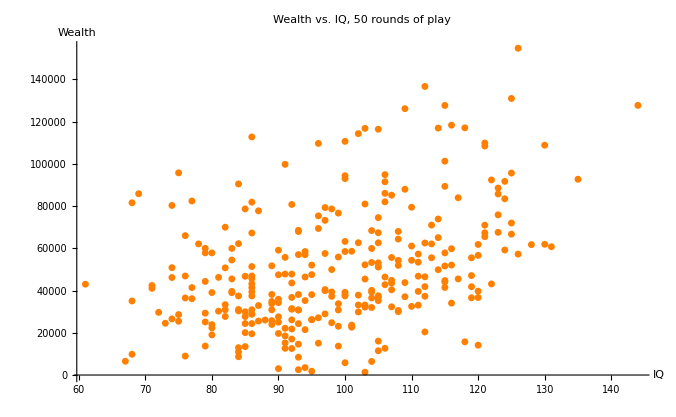

```mathematica
ListPlot[Transpose[{IqList,wealthList}],AxesLabel->{"IQ","Wealth"},PlotStyle->Orange,PlotLabel->Style["Wealth vs. IQ,\n 50 rounds of play",FontSize->24,FontColor->RGBColor[0.8,0.8,0.8]]]
```

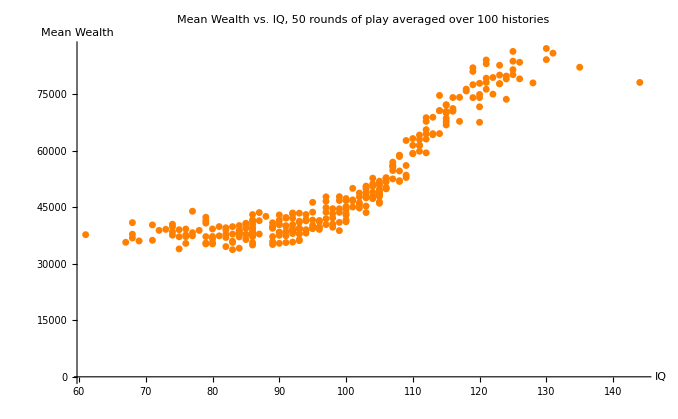

```mathematica
ListPlot[Transpose[{IqList,meanWealthList}],AxesLabel->{"IQ", "Mean Wealth"},PlotStyle->Orange,PlotLabel->Style["Mean Wealth vs. IQ,\n 50 rounds of play\n averaged over 100 histories",FontSize->24,FontColor->RGBColor[0.8,0.8,0.8]]]
```

### Strengths, Weaknesses, and Plausibility of the Model

#### Weaknesses

Lack of game evolution.

Lack of “winning it big”

All games are zero-sum

No intergenerational wealth transfers

## Analysis and Results

## Discussion